```mathematica
ClearAll["Global`*"]

(* Script outputs a rational polynomial fit of thermodynamic variables given by best eos *)
(* Copy-paste fits to equation_of_state class functions in rhic/src/EquationOfState.cpp *)

(* Functions in equation_of_state class (no argument means it's a function of energy density)*)

(* Lattice QCD functions *)
(* equilbrium_pressure() *)
(* speed_of_sound_squared() *)
(* effective_temperature() *)

(* Quasiparticle functions *)
(* z_quasi(T) *)
(* mdmde_quasi() *)
(* equilibrium_mean_field(T) *)
(* equilibrium_kinetic_pressure(T) *)

(* Shear-bulk relaxation time coefficients *)
(* where/how did I compute these??? *)
(* beta_shear(T) *)
(* beta_bulk(T) *)


Nf=3.0; (* quark flavors *)
prefactorGluons=(16. Pi^2)/30.;
prefactorQuarks=(7.* Nf * Pi^2)/20.;  
sFac = prefactorGluons + prefactorQuarks;
Print["Conformal prefactor = ", sFac];

(* plot styles *)
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

(* rational polynomial fit module *)
rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];

tempPts = 450;                                                                                                 (* temperature ranges from 50 to 500 MeV *)
wd=SetDirectory@NotebookDirectory[];
eosData=Take[Import[wd<>"/best_eos.dat"]][[1;;450]];   (* only taking Subscript[μ, B] = 0 data*)
```

Conformal prefactor = 15.6269

```mathematica
(* BEST EoS data columns *)
(* 1 = Subscript[μ, B]    [MeV]  *)
(* 2 = T     [MeV]  *)
(* 3 = P(T)  [fm^-4] *)

MeVtoInversefm =  1./197.326938;   (* convert units from MeV to fm^-1 *)
temp =MeVtoInversefm * eosData[[All,2]];
Tmin = temp[[1]];
Tmax=temp[[-1]];
pressure=eosData[[All,3]];
pressureTdata=Table[{temp[[i]],pressure[[i]]},{i,1,Length[pressure]}];

(* enforce thermodynamic consistency *)
Pfit=Interpolation[pressureTdata];
Sfit[T_]=Pfit'[T];
efit[T_]=T*Sfit[T]-Pfit[T];

Print["energy min = ",efit[Tmin]," fm^-4"]
Print["energy max = ",efit[Tmax]," fm^-4"]
Print[""]
Print["pressure min = ",Pfit[Tmin]," fm^-4"]
Print["pressure max = ",Pfit[Tmax]," fm^-4"]
```

energy min = 0.00196754 fm^-4

energy max = 523.599 fm^-4

pressure min = 0.000408923 fm^-4

pressure max = 158.987 fm^-4

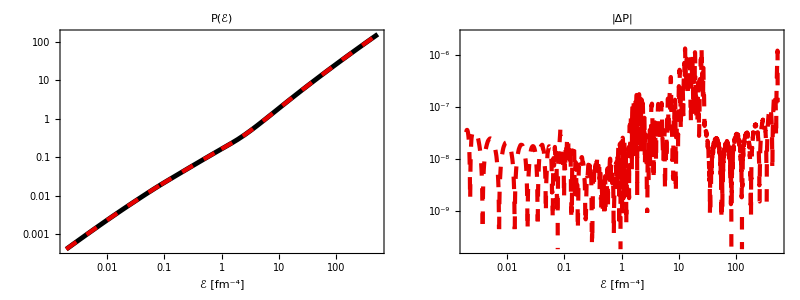

(-9.77421259885778e-9 + 0.00013479424368211223*e + 0.03671303603162032*Power(e,2) - 1.4635648045261205*Power(e,3) + 30.070461872078653*Power(e,4) - 354.74501550074666*Power(e,5) + 
     2500.4098559923796*Power(e,6) - 7993.751356286666*Power(e,7) - 16828.548663903704*Power(e,8) - 38151.175464110616*Power(e,9) + 29684.66786591466*Power(e,10) - 
     28606.19271679522*Power(e,11) + 51768.006968718706*Power(e,12) - 23304.51305297744*Power(e,13) + 31571.0774610957*Power(e,14) - 7535.526586725168*Power(e,15) + 
     10047.739435322568*Power(e,16) - 3957.4005825376826*Power(e,17) + 1975.9161615611795*Power(e,18) - 107.17731533848313*Power(e,19) + 67.12460428826888*Power(e,20) + 
     5.040973870121448*Power(e,21) + 0.08554479242275134*Power(e,22) + 0.0003907565982091207*Power(e,23) + 3.728421314866384e-7*Power(e,24))/
   (0.0006870885682005535 + 0.14205525729874968*e - 5.500592162907112*Power(e,2) + 109.19584518974632*Power(e,3) - 1216.3898276156856*Power(e,4) + 7661.10970721356*Power(e,5) - 
     13487.739351401786*Power(e,6) - 151529.00222206805*Power(e,7) - 109401.65602665946*Power(e,8) - 45153.24235832612*Power(e,9) + 69615.23328090744*Power(e,10) + 
     92152.57765840189*Power(e,11) + 38708.5875154835*Power(e,12) + 15571.535973028376*Power(e,13) + 111732.62002686801*Power(e,14) - 21386.254186412047*Power(e,15) + 
     4519.417202092523*Power(e,16) + 6369.889950434035*Power(e,17) + 221.64808772080332*Power(e,18) + 365.86233002869716*Power(e,19) + 20.99775424771206*Power(e,20) + 
     0.3046664859464902*Power(e,21) + 0.001268048472095741*Power(e,22) + 1.1486366829202303e-6*Power(e,23) - 1.8463660799680662e-12*Power(e,24))

```mathematica
(*** rational polynomial fit P(e) ***)

PdataED=Table[{efit[temp[[i]]],Pfit[temp[[i]]]},{i,1,Length[temp]}];
Pfunc=Interpolation[PdataED];

n =24;
PfitED[e_]=rationalPolyFit[PdataED,n,n]/.{x->e};

Grid[{{
LogLogPlot[{Pfunc[e],PfitED[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLogPlot[{Abs[Pfunc[e]-PfitED[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|ΔP|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
CForm[PfitED[e]]
```

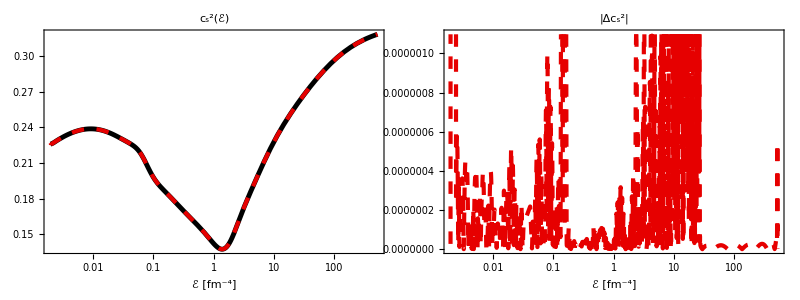

(-1.3378642078325803e-10 - 1.5950948649887635e-7*e + 0.00007945445488908329*Power(e,2) + 0.01996234704174214*Power(e,3) - 1.1125773170005704*Power(e,4) + 
     34.733370064162244*Power(e,5) - 547.7523676213551*Power(e,6) + 4138.1960309011365*Power(e,7) + 10739.20321097105*Power(e,8) - 391608.13762970857*Power(e,9) + 
     2.9203484346217643e6*Power(e,10) - 4.1009309781387197e6*Power(e,11) + 4.450746428247106e6*Power(e,12) - 3.017452573518319e6*Power(e,13) + 1.783572925370133e6*Power(e,14) - 
     650713.7960327398*Power(e,15) + 165710.3506623994*Power(e,16) - 13946.456139958056*Power(e,17) + 2741.3105420463166*Power(e,18) + 242.97782587915233*Power(e,19) + 
     3.5616970605718867*Power(e,20) - 0.003515630686533548*Power(e,21) - 7.988145364091663e-6*Power(e,22))/
   (-7.429397444705208e-10 - 5.952686470559825e-7*e + 0.0003572765249348329*Power(e,2) + 0.07449714750849573*Power(e,3) - 3.7080855166513604*Power(e,4) + 
     101.37436536443452*Power(e,5) - 1030.995434611437*Power(e,6) - 5659.823566979242*Power(e,7) + 309381.1506116967*Power(e,8) - 3.407625175874781e6*Power(e,9) + 
     1.858483682003881e7*Power(e,10) - 2.1164700434839282e7*Power(e,11) + 1.804444254502052e7*Power(e,12) - 7.632029999619695e6*Power(e,13) + 4.937094560517381e6*Power(e,14) - 
     2.1423448351671346e6*Power(e,15) + 697186.9316759608*Power(e,16) - 52684.605480706494*Power(e,17) + 13289.983630833458*Power(e,18) + 885.8789161117616*Power(e,19) + 
     10.879103743185897*Power(e,20) - 0.011317783627066228*Power(e,21) - 0.000024357749304257836*Power(e,22))

```mathematica
(*** rational polynomial fit Subscript[c, s]^2(e) ***)

(* Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= (e+p)/(T de/dT) *)
cs2temp[T_]=(efit[T]+Pfit[T])/(T*efit'[T]);
cs2data=Table[{efit[temp[[i]]],cs2temp[temp[[i]]]},{i,1,Length[temp]}];
cs2=Interpolation[cs2data];

n =22;
cs2fit[e_]=rationalPolyFit[cs2data,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{cs2[e],cs2fit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogLinearPlot[{Abs[cs2[e]-cs2fit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|Δc_s^2|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

CForm[cs2fit[e]]
```

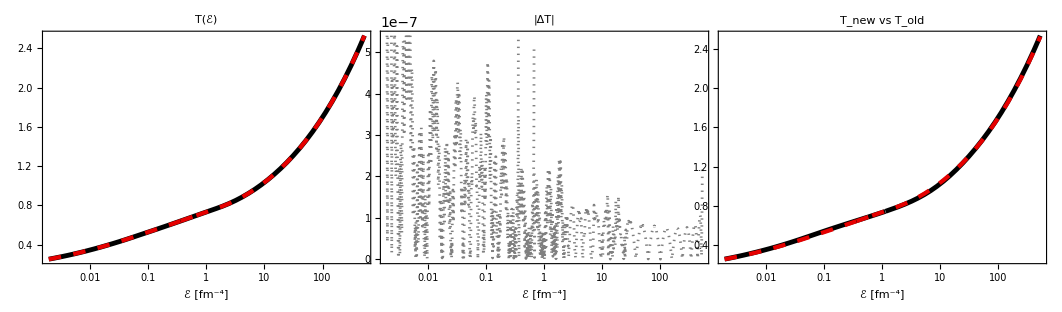

(5.673544485089304e-7 + 0.0014502942511073734*e + 0.4088351660476373*Power(e,2) + 
     12.824356109713193*Power(e,3) - 272.2193761418479*Power(e,4) + 
     2010.137345776696*Power(e,5) + 22865.55750084165*Power(e,6) - 
     108295.31775260474*Power(e,7) + 94277.78688565874*Power(e,8) + 
     1703.6016078380371*Power(e,9) + 18534.920321058595*Power(e,10) - 
     37544.20850043495*Power(e,11) - 1605.3283866459035*Power(e,12) + 
     111939.85077697897*Power(e,13) - 32548.05168701283*Power(e,14) + 
     4819.378867151488*Power(e,15) + 5812.584002307635*Power(e,16) + 
     294.814561826252*Power(e,17) + 3.2942364751359157*Power(e,18) + 
     0.008451012193304464*Power(e,19) + 3.408452078337276e-6*Power(e,20))/
   (3.7098708367987744e-6 + 0.00601666825252551*e + 1.1471670105742588*Power(e,2) + 
     17.803008957876514*Power(e,3) - 556.0834473853861*Power(e,4) + 
     6089.219405252193*Power(e,5) + 21772.237662792355*Power(e,6) - 
     151503.0699694077*Power(e,7) + 156296.5167566047*Power(e,8) - 
     655.2433134298738*Power(e,9) - 32536.428770670453*Power(e,10) + 
     34541.518012795874*Power(e,11) - 62522.216221383256*Power(e,12) + 
     187530.57287111995*Power(e,13) - 68478.59270513344*Power(e,14) + 
     15837.894670632597*Power(e,15) + 5765.165860783288*Power(e,16) + 
     204.11631027023358*Power(e,17) + 1.616419010123996*Power(e,18) + 
     0.0027912062900649856*Power(e,19) + 5.990097671463406e-7*Power(e,20))

```mathematica
(*** T(e) ***)

efit[0.155*5.067731];

TdataED=Table[{efit[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];

Tfunc=Interpolation[TdataED];

n =20;

Tfit[e_]=rationalPolyFit[TdataED,n,n]/.{x->e};

Told[e_]=(2.059151308901543*10^-66+1.2883117551723254*10^-37*e+9.653685304732326*10^-18*e^2+0.0021387548523685764*e^3+3.152348276671561*10^7*e^4+6.128861811040275*10^14*e^5+1.2611913502159628*10^20*e^6+8.510311640702168*10^23*e^7+3.3406440917885196*10^26*e^8+9.526824863039937*10^27*e^9-5.540454604707275*10^27*e^10-3.834326779020863*10^28*e^11+2.732286036998176*10^28*e^12+3.389763887380034*10^27*e^13+3.271304177799644*10^25*e^14+3.5796316255209677*10^22*e^15+3.647754101481452*10^18*e^16)/(3.465150960288193*10^-64+7.292333136125966*10^-36*e+3.167120708990754*10^-16*e^2+0.047875501682141906*e^3+5.1924910033740276*10^8*e^4+7.186120863411006*10^15*e^5+9.741960860767537*10^20*e^6+3.9749426686364564*10^24*e^7+9.163047659503782*10^26*e^8+1.4902973847933083*10^28*e^9-1.710867316101183*10^28*e^10-4.366544624555957*10^28*e^11+3.801696016710178*10^28*e^12+2.43514662137169*10^27*e^13+1.376570820431094*10^25*e^14+8.761759990161081*10^21*e^15+4.265493796252328*10^17*e^16);

GraphicsGrid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Abs[Tfunc[e]-Tfit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["|ΔT|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],

LogLinearPlot[{Told[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->400,Frame->True,PlotLabel->Style["T_new vs T_old",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}},Spacings->{-50,0}]

CForm[Tfit[e]]
```

1.38708

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

1.38708

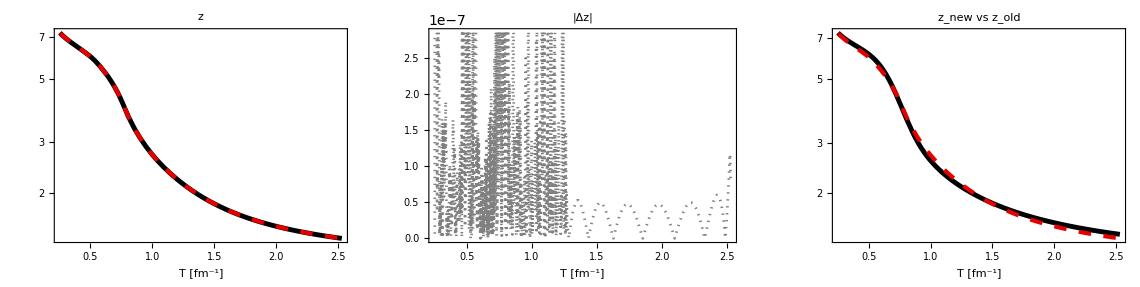

(-0.017949824450839202 + 0.3365732529575597*T - 3.140027482980438*Power(T,2) + 
     19.150986821286097*Power(T,3) - 80.32828096873735*Power(T,4) + 
     223.0568811801298*Power(T,5) - 357.5705165180529*Power(T,6) + 
     137.25352080053486*Power(T,7) + 600.7325894830118*Power(T,8) - 
     882.90137770045*Power(T,9) - 704.985543206264*Power(T,10) + 
     2847.143162755488*Power(T,11) - 1434.669360650123*Power(T,12) - 
     3621.720727049755*Power(T,13) + 5217.239280673325*Power(T,14) + 
     1003.7234905704108*Power(T,15) - 8176.736982411804*Power(T,16) + 
     7551.239421807917*Power(T,17) - 998.8427262787882*Power(T,18) - 
     3478.2143705639182*Power(T,19) + 3191.8910303933458*Power(T,20) - 
     1254.4250207926118*Power(T,21) + 201.81079631224793*Power(T,22))/
   (-0.0008786405033750089 + 0.008268152320595109*T - 0.014355266876850408*Power(T,2) - 
     0.15086506871871244*Power(T,3) + 1.3944986778697523*Power(T,4) - 
     7.405567644760638*Power(T,5) + 26.529849132299145*Power(T,6) - 
     54.07651514860081*Power(T,7) + 22.91053466954111*Power(T,8) + 
     155.5443369295718*Power(T,9) - 306.9510409366884*Power(T,10) - 
     79.78818018912837*Power(T,11) + 932.423018816308*Power(T,12) - 
     794.8364978929295*Power(T,13) - 1282.9020196284453*Power(T,14) + 
     2872.9335015055467*Power(T,15) - 200.70897006828687*Power(T,16) - 
     5991.549508073676*Power(T,17) + 10191.814369998257*Power(T,18) - 
     9007.723415241728*Power(T,19) + 4789.057107227963*Power(T,20) - 
     1469.628261044679*Power(T,21) + 203.1297371594139*Power(T,22))

```mathematica
(*** z(T) ***)

nc = 3.0;
nf = 3.0;
g =Pi^4/180.0*(4.0*(nc^2-1.0)+7.0*nc*nf);
F[T_]=(2.0*Pi^2)/g*Sfit[T]/T^3;

zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];

zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[450]]],{x,1.3},MaxIterations->5000]

For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]

zQuasifunc=Interpolation[zQuasi];

zQuasidata=Table[{T,zQuasifunc[T]},{T,Tmin,Tmax, 0.005067731}];

n = 22;

zQuasifit[T_]=rationalPolyFit[zQuasidata,n,n]/.{x->T};

zQuasifit[temp[[450]]]


zold[T_]=(2.195527549421445*10^-14+5.014273212142939*10^-11*T+6.8769768080936324*10^-9*T^2-1.3090323372462384*10^-6*T^3+0.00007503723419734601*T^4-0.0019335423100477788*T^5+0.0077581370622797526*T^6+1.0840238709953247*T^7-40.41237726417249*T^8+815.5709414412947*T^9-11117.3113417968*T^10+107720.35990943392*T^11-727161.0603316505*T^12+3.12288627176472*10^6*T^13-7.240727201149486*10^6*T^14+8.813651470346985*10^6*T^15-3.535759885234317*10^6*T^16-5.454281769326236*10^6*T^17+1.0415987187648855*10^7*T^18-8.0189396235499745*10^6*T^19+2.6430627991581215*10^6*T^20)/(1.1541703277540495*10^-16+4.122377967105372*10^-13*T+1.2528690762234088*10^-10*T^2-1.1203883703791743*10^-8*T^3-3.65428489042621*10^-8*T^4+0.00004068369176438496*T^5-0.0024580222716044254*T^6+0.08433957015198745*T^7-2.0279246693088906*T^8+36.56366190486074*T^9-490.05025567116945*T^10+4477.3308927313055*T^11-21467.525530376926*T^12-23929.310531648207*T^13+889228.088912891*T^14-4.262596231414713*10^6*T^15+1.0642287968093066*10^7*T^16-1.643826578603126*10^7*T^17+1.6160269998993594*10^7*T^18-9.40765741315934*10^6*T^19+2.502796051035953*10^6*T^20);

GraphicsGrid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

Plot[{Abs[zQuasifunc[T]-zQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δz|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],

LogPlot[{zold[T],zQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["z_new vs z_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

zQuasifit[T]//CForm
```

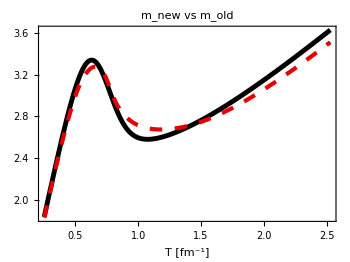

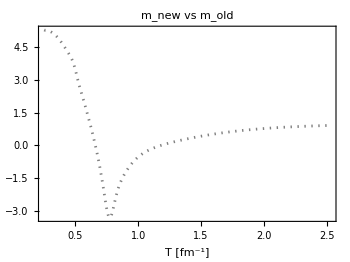

```mathematica
mQuasifunc[T_] =T*zQuasifunc[T]; 

Plot[{T*zold[T],mQuasifunc[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m_new vs m_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

Plot[{mQuasifunc'[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["m_new vs m_old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

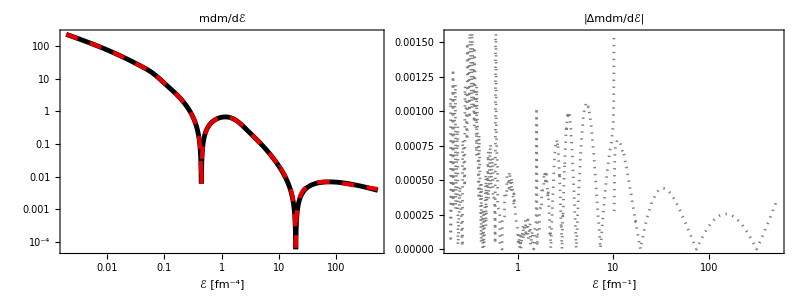

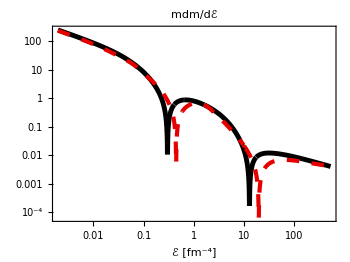

(-0.000031056665345165724 + 0.016791463729416135*e + 3.4678582470540937*Power(e,2) - 
     104.4989344442848*Power(e,3) + 1606.8850603283322*Power(e,4) - 
     13168.391352937877*Power(e,5) + 78996.30644857828*Power(e,6) - 
     118812.51389215932*Power(e,7) - 59593.39532137042*Power(e,8) - 
     3138.110739412731*Power(e,9) + 112509.8805383922*Power(e,10) + 
     176825.1969463141*Power(e,11) + 118108.5856680918*Power(e,12) + 
     10319.664108353432*Power(e,13) - 22247.709772597842*Power(e,14) - 
     8570.602864214365*Power(e,15) - 1792.3527292793178*Power(e,16) - 
     5403.751999227621*Power(e,17) - 8860.677015090665*Power(e,18) - 
     5150.17018870056*Power(e,19) + 2154.9476297698075*Power(e,20) + 
     2199.47011775134*Power(e,21) - 753.3684787908472*Power(e,22) - 
     102.9371303482576*Power(e,23) + 23.549385629912443*Power(e,24) - 
     0.7952122782853916*Power(e,25) - 0.0028734664734872202*Power(e,26))/
   (-4.796980084586926e-8 - 0.000027837510425536854*e + 0.03928886986912415*Power(e,2) + 
     1.854876565065449*Power(e,3) - 43.843513929376755*Power(e,4) + 
     260.364257145724*Power(e,5) + 3345.9186169872537*Power(e,6) - 
     25062.68960092198*Power(e,7) + 262360.9497468116*Power(e,8) - 
     208096.98980643332*Power(e,9) - 229686.2098651997*Power(e,10) - 
     99585.48207002637*Power(e,11) - 59356.15425484898*Power(e,12) - 
     39680.62243774634*Power(e,13) - 15864.464294462641*Power(e,14) + 
     538.5411274085207*Power(e,15) + 6827.013290155933*Power(e,16) + 
     7102.3428999115895*Power(e,17) + 5087.808147358985*Power(e,18) + 
     2905.5142675835646*Power(e,19) + 1656.5746794756537*Power(e,20) + 
     1406.0870166172385*Power(e,21) + 641.7405147061494*Power(e,22) - 
     1851.027725021699*Power(e,23) + 690.5877395897703*Power(e,24) - 
     40.931514140034174*Power(e,25) - 0.9658155192728282*Power(e,26))

```mathematica
(*** m(e) and dm/de ***) 

mdataED=Table[{efit[temp[[i]]],temp[[i]]*zQuasifunc[temp[[i]]]},{i,1,Length[temp]}];

mfunc=Interpolation[mdataED];

mdmde[e_]=mfunc[e]*mfunc'[e];

mdmdedata=Table[{efit[temp[[i]]],mdmde[efit[temp[[i]]]]},{i,1,Length[temp]}];

n =26;

mdmdefit[e_]=rationalPolyFit[mdmdedata,n,n]/.{x->e};

mdmdeold[e_]=(1.0932938963420931*10^-38-1.007252920091783*10^-31*e+1.258073500377669*10^-25*e^2+3.7902939287037426*10^-19*e^3+9.982754875153906*10^-14*e^4+5.356830067926448*10^-9*e^5+0.00006631556444292836*e^6+0.19429591145238154*e^7+133.14135704995198*e^8+19906.496386848434*e^9+468502.08289765124*e^10-2.1057407552865325*10^6*e^11-3.1682608543291925*10^6*e^12+1.7046132756833293*10^7*e^13-1.3636657914477058*10^7*e^14+2.0863251242849804*10^7*e^15-2.0496583087455064*10^7*e^16-4.069098068002096*10^7*e^17+3.445677209399048*10^7*e^18-3.7295352481362685*10^6*e^19+212848.6045508894*e^20-15965.651067054185*e^21+532.5403558600549*e^22+2.411729540242231*e^23+0.00027216645617684197*e^24)/(1.8097473184974786*10^-43-1.1919700038034044*10^-36*e-2.880545193459095*10^-30*e^2+1.5774335161251585*10^-23*e^3+1.2056411612584795*10^-17*e^4+1.5859303052883873*10^-12*e^5+4.642427449619644*10^-8*e^6+0.0003211322658208788*e^7+0.5307842016671973*e^8+205.22641687449376*e^9+17197.020001063076*e^10+262076.7134892617*e^11+1.517168279215402*10^6*e^12-4.41387607180566*10^6*e^13-4.689689648983293*10^6*e^14-1.1727564734279385*10^6*e^15+4.517859607565268*10^6*e^16+1.8472203478591543*10^7*e^17+1.8233835956962608*10^7*e^18-2.052678068458237*10^7*e^19+1.7590273805695719*10^6*e^20-448178.89154244727*e^21+13727.684912668212*e^22+572.3076682226775*e^23+0.5135708549693685*e^24);


Grid[{{LogLogPlot[{Abs[mdmde[e]],Abs[mdmdefit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLinearPlot[{Abs[mdmde[e]-mdmdefit[e]]},{e,100emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δmdm/dℰ|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

LogLogPlot[{Abs[mdmdeold[e]],Abs[mdmdefit[e]]},{e,emin,emax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]

mdmdefit[e]//CForm
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

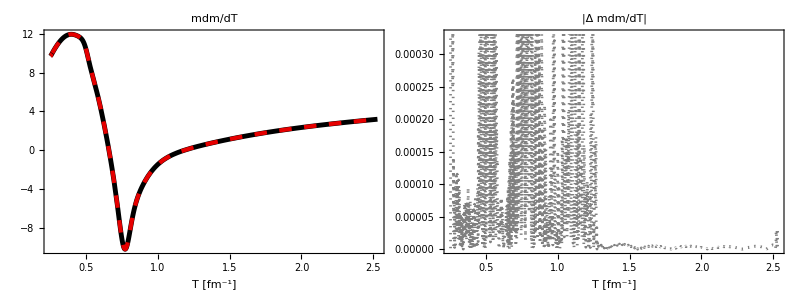

(0.008620204990765936 - 0.1915323482819938*T + 1.8699991821501438*Power(T,2) - 
     9.725907782526928*Power(T,3) + 20.891937868587675*Power(T,4) + 
     62.16205531233371*Power(T,5) - 617.8941863334413*Power(T,6) + 
     2094.838890855853*Power(T,7) - 3476.8787505920905*Power(T,8) + 
     1193.8777642713499*Power(T,9) + 5506.516188202346*Power(T,10) - 
     5844.946027650698*Power(T,11) - 11680.145452131916*Power(T,12) + 
     28100.706052853704*Power(T,13) - 2198.510394919234*Power(T,14) - 
     59604.98523414622*Power(T,15) + 82417.42732045021*Power(T,16) - 
     20192.814381847173*Power(T,17) - 71613.41301554958*Power(T,18) + 
     110210.5573064508*Power(T,19) - 84562.12309679275*Power(T,20) + 
     40595.21854871077*Power(T,21) - 12514.650567747625*Power(T,22) + 
     2307.274616325548*Power(T,23) - 195.07648955983245*Power(T,24))/
   (0.002688192590188464 - 0.07234735438582685*T + 0.9044696302265126*Power(T,2) - 
     6.882395535617806*Power(T,3) + 34.887954991240385*Power(T,4) - 
     120.34522040485068*Power(T,5) + 271.215667375589*Power(T,6) - 
     323.345243257398*Power(T,7) - 106.80289676015616*Power(T,8) + 
     1091.35486278025*Power(T,9) - 1540.520621021885*Power(T,10) - 
     88.40011910116584*Power(T,11) + 2878.9590727414566*Power(T,12) - 
     2756.0546391981748*Power(T,13) - 2199.7845884672843*Power(T,14) + 
     7248.885437845537*Power(T,15) - 6404.875406612116*Power(T,16) + 
     875.4872012855749*Power(T,17) + 3056.476923978928*Power(T,18) - 
     2725.0789752746978*Power(T,19) + 691.5638542006817*Power(T,20) + 
     394.0936995249615*Power(T,21) - 384.3711134968192*Power(T,22) + 
     129.27634957645813*Power(T,23) - 16.57067539622674*Power(T,24))

```mathematica
(*** m dm/dT ***) 

mQuasifunc[T_] =T*zQuasifunc[T]; 

mdmdTQuasi[T_] = mQuasifunc[T] *D[ mQuasifunc[T],T];

(*mdmdTQuasi[T_] = mQuasifunc[T]*(zQuasifunc[T]+T*zQuasifunc'[T]);*)

mdmdTQuasidata=Table[{temp[[i]],mdmdTQuasi[temp[[i]]]},{i,1,Length[temp]}];

n = 24;

mdmdTQuasifit[T_]=rationalPolyFit[mdmdTQuasidata,n,n]/.{x->T};
Grid[{{
Plot[{mdmdTQuasi[T],mdmdTQuasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["mdm/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[mdmdTQuasi[T]-mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δ mdm/dT|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

mdmdTQuasifit[T]//CForm
```

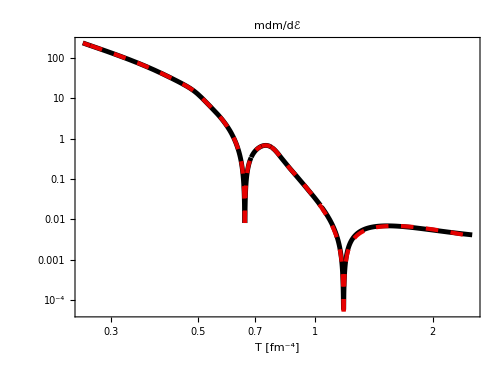

```mathematica
(*** check chain rule in relation: dm/de = cs2/s dm/dT ***)

LogLogPlot[{Abs[mdmdefit[efit[T]]],Abs[cs2fit[efit[T]]/Sfit[T]*mdmdTQuasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->500,Frame->True,PlotLabel->Style["mdm/dℰ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-4]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

-11.5778

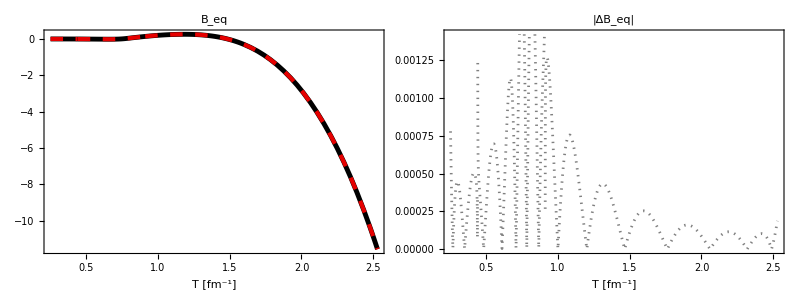

(-7.207853272499367 + 62.51732417867076*T - 117.93316245605544*Power(T,2) - 
     327.0294465450976*Power(T,3) + 1165.0077580029072*Power(T,4) - 
     23.350765703977967*Power(T,5) - 2178.0227107408555*Power(T,6) - 
     440.5242523386634*Power(T,7) + 2589.129621682232*Power(T,8) + 
     2072.3857959828197*Power(T,9) - 820.0788687930111*Power(T,10) - 
     2565.3403530889063*Power(T,11) - 1794.8244381382501*Power(T,12) + 
     193.26739767162857*Power(T,13) + 1420.420658524867*Power(T,14) + 
     1126.8446596550214*Power(T,15) + 151.27128111106435*Power(T,16) - 
     281.43344707018707*Power(T,17) - 17.36530552687749*Power(T,18) + 
     162.61594282121715*Power(T,19) - 222.88543336218848*Power(T,20))/
   (-68.49715840337487 + 726.8139379569196*T - 774.6324037518872*Power(T,2) - 
     2035.1593386044628*Power(T,3) + 147.14090328897868*Power(T,4) + 
     3262.525464579394*Power(T,5) + 3112.83741778911*Power(T,6) - 
     451.7126534017275*Power(T,7) - 3836.7427497250233*Power(T,8) - 
     3982.3451014527955*Power(T,9) - 1097.5547441310555*Power(T,10) + 
     1980.5008193478866*Power(T,11) + 2232.4485625955513*Power(T,12) + 
     1117.0597084384985*Power(T,13) + 149.62826890403227*Power(T,14) - 
     58.13108869785364*Power(T,15) + 158.25765631170873*Power(T,16) + 
     176.60547337535198*Power(T,17) - 7.631957692979938*Power(T,18) - 
     13.735345089101*Power(T,19) + 2.452299648657458*Power(T,20))

```mathematica
(*** Subscript[B, eq](T) alternative ***)

n = 20;
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];

B0Quasi2=Table[{temp[[i]],Pquasi[temp[[i]]]-Pfit[temp[[i]]]},{i,1,Length[temp]}];

B0Quasifunc2=Interpolation[B0Quasi2];

B0Quasifit2[T_]=rationalPolyFit[B0Quasi2,n,n]/.{x->T};

B0Quasifit2[temp[[450]]]

Grid[{{
Plot[{B0Quasifunc2[T],B0Quasifit2[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[B0Quasifunc2[T]-B0Quasifit2[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

B0Quasifit2[T]//CForm

(* It's probably more accurate to calculate B this way *)
```

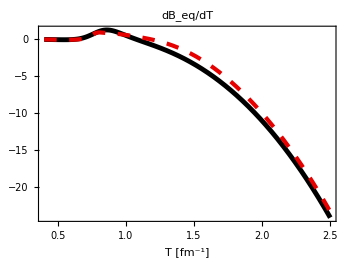

```mathematica
dmdTQuasi[T_]=mQuasifunc'[T];

mold[T_]=T*zold[T];

dmdTold[T_]=mold'[T];

H[T_] = -(g*T*mQuasifunc[T]*BesselK[1,zQuasifit[T]]*mdmdTQuasi[T])/(2.0*Pi^2);


H2[T_]=D[Pquasi[T]-Pfit[T],T];

Hfuncold[T_]=-(g*T^3*zold[T]^2*BesselK[1,zold[T]]*dmdTold[T])/(2.0*Pi^2);

Plot[{Hfuncold[T],H[T]},{T,.4,0.99temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["dB_eq/dT",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

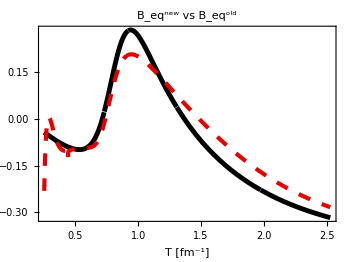

```mathematica
Beqold[T_]=(-0.003259287424704517+0.4709321130178677*T-18.471027719937705*T^2+334.0690722721871*T^3-3454.385244668648*T^4+22960.15979638924*T^5-105315.46668675772*T^6+346561.90522823617*T^7-836638.407629094*T^8+1.501743414016609*10^6*T^9-2.020237220416*10^6*T^10+2.0480693209160143*10^6*T^11-1.5779382837830463*10^6*T^12+943559.9448756306*T^13-456516.3985230772*T^14+185756.11302939596*T^15-61106.69072505601*T^16+13705.921942194844*T^17-1465.8180676090112*T^18)/(294.675932969415-1745.8088045773043*T+3997.025794070807*T^2-3586.7652790072334*T^3-1117.8588245192668*T^4+3765.9359654630407*T^5+841.4750390325167*T^6-4142.400568278239*T^7-1464.515167915579*T^8+4738.833500521431*T^9+2188.180519746309*T^10-6031.500378704362*T^11-203.76274436224986*T^12+5225.119313817963*T^13-3608.5761295285674*T^14+927.278254033823*T^15-80.77885500958108*T^16+4.197658993150538*T^17-0.10024694968615945*T^18);

Plot[{Beqold[T]/T^4,B0Quasifit2[T]/T^4},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq^new vs B_eq^old",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
```

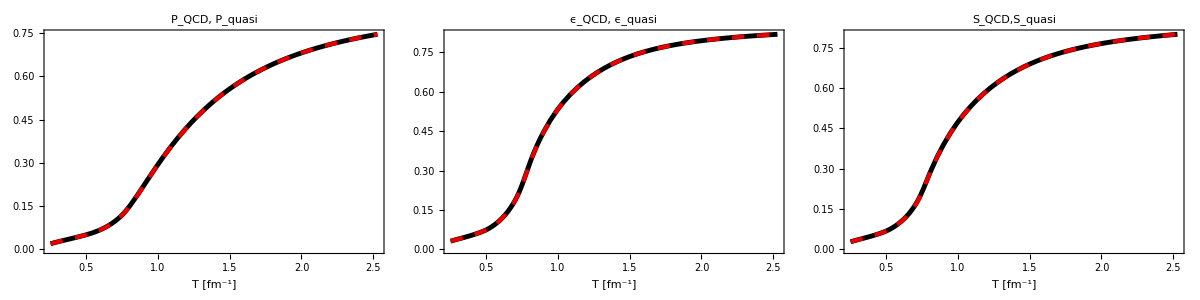

```mathematica
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -B0Quasifunc2[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+B0Quasifunc2[T];

SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{Plot[{Pfit[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{efit[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Sfit[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

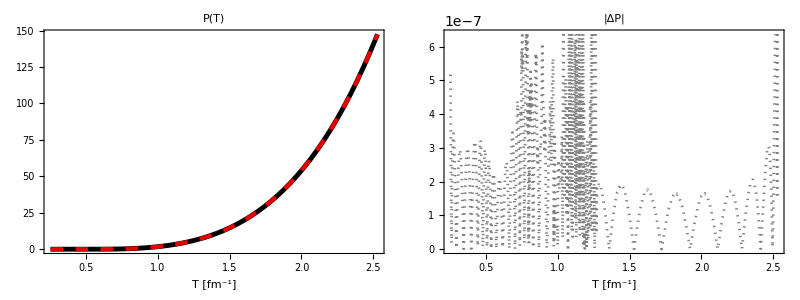

(0.1442299621888816 - 3.6105109252546375*T + 40.956433747951145*Power(T,2) - 
     280.54493637161806*Power(T,3) + 1307.1552747202693*Power(T,4) - 
     4425.8319316418565*Power(T,5) + 11383.965179966624*Power(T,6) - 
     23031.02528124637*Power(T,7) + 37633.78172295909*Power(T,8) - 
     50212.60864583127*Power(T,9) + 53880.25150874668*Power(T,10) - 
     44411.79139931206*Power(T,11) + 26004.890361611033*Power(T,12) - 
     9494.117196119518*Power(T,13) + 1608.7846767833507*Power(T,14))/
   (72.48650513902498 - 939.9725763374905*T + 5536.218584089283*Power(T,2) - 
     19597.506368209244*Power(T,3) + 46485.48039005736*Power(T,4) - 
     77960.05374586156*Power(T,5) + 95014.90157525778*Power(T,6) - 
     85110.09620539528*Power(T,7) + 55971.25705070983*Power(T,8) - 
     26717.242410808714*Power(T,9) + 9103.469312318051*Power(T,10) - 
     2193.6328190004365*Power(T,11) + 371.0244542736764*Power(T,12) - 
     37.864681988206605*Power(T,13) + 1.7619827904681449*Power(T,14))

```mathematica
(* Fitting the quasiparticle kinetic pressure (B = 0) *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]];  (*kinetic only; no bag term*)
Pquasidata=Table[{temp[[i]],Pquasi[temp[[i]]]},{i,1,Length[temp]}];
n = 14;
Pquasifit[T_]=rationalPolyFit[Pquasidata,n,n]/.{x->T};

Grid[{{
Plot[{Pquasi[T],Pquasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["P(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Pquasi[T]-Pquasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔP|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Pquasifit[T]//CForm
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

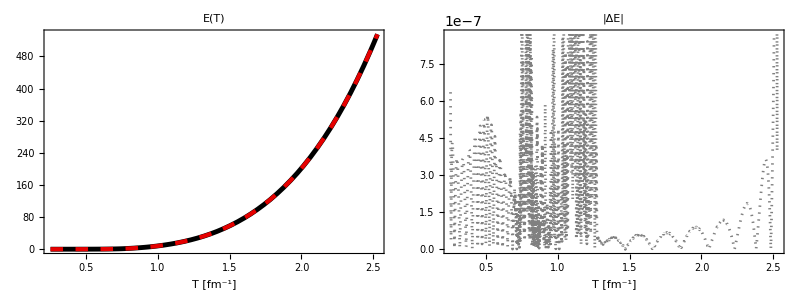

(-0.029229316142613527 + 0.8511058580313572*T - 11.202863745968656*Power(T,2) + 
     87.71383260560691*Power(T,3) - 451.3361099717664*Power(T,4) + 
     1584.8902268766908*Power(T,5) - 3769.764330257308*Power(T,6) + 
     5573.603161947856*Power(T,7) - 3122.3676488671385*Power(T,8) - 
     5571.675466168965*Power(T,9) + 13029.320543580503*Power(T,10) - 
     5586.61137787447*Power(T,11) - 16443.933335435308*Power(T,12) + 
     28622.033104511316*Power(T,13) - 8751.776262028905*Power(T,14) - 
     30645.039181034594*Power(T,15) + 54675.92814745106*Power(T,16) - 
     47672.16205836581*Power(T,17) + 25075.780787712763*Power(T,18) - 
     7700.2537716619045*Power(T,19) + 1076.0601184793243*Power(T,20))/
   (1.1004498491632229 - 15.339086797586326*T + 97.6484021552244*Power(T,2) - 
     374.2508642377322*Power(T,3) + 951.1817381074258*Power(T,4) - 
     1635.6270710853096*Power(T,5) + 1767.4752145984114*Power(T,6) - 
     713.191959391843*Power(T,7) - 1089.0440672824852*Power(T,8) + 
     1895.8518575331964*Power(T,9) - 314.1394454589418*Power(T,10) - 
     2756.0518237383008*Power(T,11) + 4784.442196082358*Power(T,12) - 
     4400.411135077415*Power(T,13) + 2576.9075164127225*Power(T,14) - 
     981.6919160518303*Power(T,15) + 241.23010902501755*Power(T,16) - 
     42.74285166271293*Power(T,17) + 7.387209564968234*Power(T,18) - 
     0.766986825107917*Power(T,19) + 0.036124789789971044*Power(T,20))

```mathematica
(* Fitting the quasiparticle kinetic energy density (B = 0) *)
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]]);  (*kinetic only; no bag term*)
Equasidata=Table[{temp[[i]],Equasi[temp[[i]]]},{i,1,Length[temp]}];
n = 20;
Equasifit[T_]=rationalPolyFit[Equasidata,n,n]/.{x->T};
Grid[{{
Plot[{Equasi[T],Equasifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["E(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Equasi[T]-Equasifit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔE|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
Equasifit[T]//CForm
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

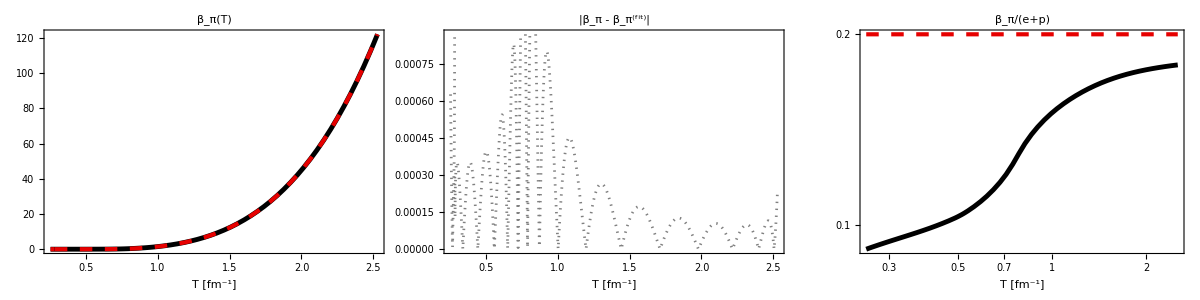

(-4.559186863959626 + 69.86334705250142*T - 425.07528354326666*Power(T,2) + 
     1268.059768668576*Power(T,3) - 1739.0260845778541*Power(T,4) + 
     356.80703482226835*Power(T,5) + 1303.8002405853554*Power(T,6) - 
     224.91212390972507*Power(T,7) - 900.6603057381708*Power(T,8) - 
     307.3985521264842*Power(T,9) + 303.35215554381773*Power(T,10) + 
     335.54179834641616*Power(T,11) + 99.6613576951631*Power(T,12) - 
     12.693372341662348*Power(T,13) + 24.77073181998932*Power(T,14))/
   (-15.35026621554268 + 48.7412789585087*T + 53.69554937572056*Power(T,2) - 
     84.82154942062445*Power(T,3) - 143.89514714218154*Power(T,4) + 
     29.92699172555165*Power(T,5) + 110.28001697309789*Power(T,6) + 
     60.71726923701555*Power(T,7) + 17.679870475805952*Power(T,8) + 
     15.107230793738804*Power(T,9) + 9.865144767539169*Power(T,10) - 
     1.4431339740643492*Power(T,11) - 2.060536863228295*Power(T,12) + 
     1.049091511320209*Power(T,13) - 0.1370012959279261*Power(T,14))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 14;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*Sfit[T]*T;

Grid[{{Plot[{betapi[T],betapifit[T]},{T,temp[[1]],temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

122.159

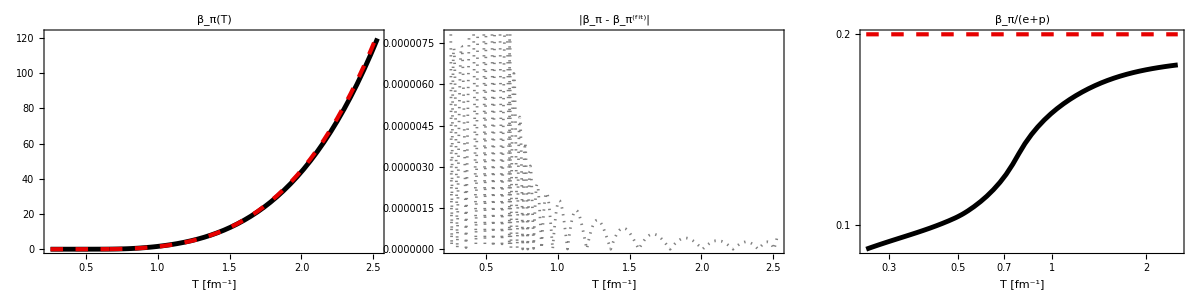

(0.2136366760211705 - 3.340576648101186*T + 20.35617723895945*Power(T,2) - 
     56.437960482829034*Power(T,3) + 44.289349037853*Power(T,4) + 
     110.38570263916569*Power(T,5) - 192.64743429589146*Power(T,6) - 
     139.2039704101172*Power(T,7) + 292.55870523679425*Power(T,8) + 
     365.04203673033663*Power(T,9) - 320.9965086154278*Power(T,10) - 
     959.4522456504616*Power(T,11) + 388.3661328011906*Power(T,12) + 
     1895.9070095452914*Power(T,13) - 1081.7606276754307*Power(T,14) - 
     3073.63080222343*Power(T,15) + 5690.12244645798*Power(T,16) - 
     4289.66257583748*Power(T,17) + 1319.182225500954*Power(T,18))/
   (-8.42333665536514 + 34.60163009640503*T - 40.80874190893032*Power(T,2) - 
     37.97142299728571*Power(T,3) + 134.6544464825261*Power(T,4) + 
     9.706531768837149*Power(T,5) - 255.7132495167302*Power(T,6) - 
     99.03328376529788*Power(T,7) + 539.9754265932293*Power(T,8) + 
     292.78802164155434*Power(T,9) - 1271.0364139156522*Power(T,10) + 
     422.9829584085978*Power(T,11) + 1196.0787054290631*Power(T,12) - 
     1538.6207084629368*Power(T,13) + 751.2670591504994*Power(T,14) - 
     157.80341029086318*Power(T,15) + 38.4721244970019*Power(T,16) - 
     5.155456445839421*Power(T,17) + 0.29607127346088863*Power(T,18))

```mathematica
betapiDataRaw=Import[wd<>"/betapiplot.dat"];
betapiData= Take[betapiDataRaw,{2,Length[betapiDataRaw]}];
betapi = Interpolation[betapiData[[All,{1,2}]]];
n = 18;
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapiconformal[T_]=0.2*T*Sfit[T];

betapifit[temp[[450]]]

betapiold[T_]=(8.611704298094825*10^-6-0.001405354006113392*T+0.059924402660583354*T^2-1.1252821226321765*T^3+11.505088678768702*T^4-72.86243933500441*T^5+312.67652000568955*T^6-919.4553300642775*T^7+1851.880055174282*T^8-2520.2910195876684*T^9+2228.4719999229687*T^10-1163.3696941415265*T^11+275.1649200477449*T^12)/(4.814184219646834-23.427763291345297*T+78.10907293901035*T^2-220.9834748507111*T^3+463.6211365026477*T^4-658.0962754530466*T^5+604.0491642749903*T^6-329.15455711633166*T^7+83.03984882593176*T^8-0.34262854377950497*T^9+0.03765047242502595*T^10-0.0024572359354327667*T^11+0.0000720828838022736*T^12);

Grid[{{Plot[{betapiold[T],betapifit[T]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betapi[T]-betapifit[T]]},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|β_π - β_π^(fit)|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{betapi[T]/(T*Sfit[T]),betapiconformal[T]/(T*Sfit[T])},{T,Tmin,temp[[450]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
betapifit[T]//CForm
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

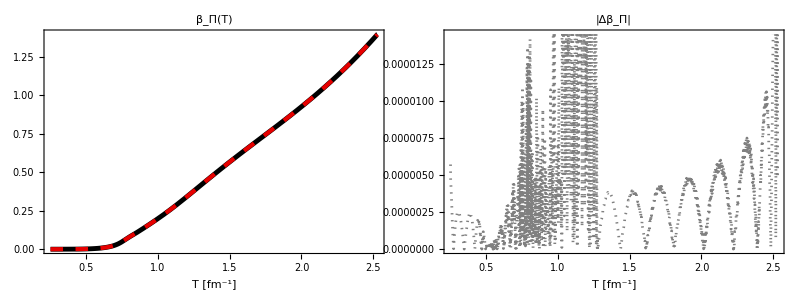

(0.026481529867662307 - 0.6111772972588377*T + 6.343210579556402*Power(T,2) - 
     38.79623447342289*Power(T,3) + 153.24490431060164*Power(T,4) - 
     397.6140880918454*Power(T,5) + 632.0903925395189*Power(T,6) - 
     391.8990663517056*Power(T,7) - 655.7686822427216*Power(T,8) + 
     1739.8416623617422*Power(T,9) - 1122.4992696730747*Power(T,10) - 
     1754.4122956461954*Power(T,11) + 4846.080642732388*Power(T,12) - 
     5612.075872972241*Power(T,13) + 3963.0180450684607*Power(T,14) - 
     1808.8523728764505*Power(T,15) + 522.5549318287887*Power(T,16) - 
     87.03575609379466*Power(T,17) + 6.367816284680329*Power(T,18))/
   (26.674662968700844 - 319.7255476285733*T + 1635.7015285864773*Power(T,2) - 
     4520.860700050181*Power(T,3) + 6718.377321595138*Power(T,4) - 
     3237.61968843591*Power(T,5) - 5607.683143059901*Power(T,6) + 
     8899.954830214761*Power(T,7) + 1244.9167711970188*Power(T,8) - 
     13560.666480763612*Power(T,9) + 10435.939947632332*Power(T,10) + 
     6367.829306822181*Power(T,11) - 18979.488963543005*Power(T,12) + 
     18103.90126513476*Power(T,13) - 10065.035552884361*Power(T,14) + 
     3544.3290140791314*Power(T,15) - 778.2950932873632*Power(T,16) + 
     96.95873025803985*Power(T,17) - 5.19171705393362*Power(T,18))

```mathematica
(* betabulk =5.0*betapi/3.0-cs2*(e+p)+cs2*mdmdT*I11 *)

Clear[betabulk,betabulkData,betabulkfit,I11DataRaw,I11Data,I11]

I11DataRaw=Import[wd<>"/betabulkplot.dat"];
I11Data= Take[I11DataRaw,{2,Length[I11DataRaw]}];
I11 = Interpolation[I11Data[[All,{1,2}]]];

betabulk[T_]=5.0/3.0*betapi[T]+cs2fit[efit[T]]*(mdmdTQuasi[T]*I11[T]-(efit[T]+Pfit[T]));

betabulkData=Table[{T,betabulk[T]},{T,Tmin,Tmax,0.001}];
betabulk=Interpolation[betabulkData];

n = 18;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};


betabulkold[T_]=(0.057187918268175174-2.5795110808844144*T+31.966143337661794*T^2-186.97202223464143*T^3+632.9739160169219*T^4-1356.8644912535221*T^5+1937.6556428262882*T^6-1901.4144609887912*T^7+1305.7115016142484*T^8-632.7107309491553*T^9+215.7883928137199*T^10-50.783337922429304*T^11+7.882963305898372*T^12-0.7302386364254765*T^13+0.031006456705249083*T^14)/(2168.5818494848654-17367.372494454743*T+62866.89323544513*T^2-136008.52657020878*T^3+196076.0893015133*T^4-198954.9682758633*T^5+146384.87731197142*T^6-79310.95783243925*T^7+31803.091369445476*T^8-9398.242646642117*T^9+2016.6245278736917*T^10-304.98512854363526*T^11+30.758339605713708*T^12-1.852389925261096*T^13+0.05027444936020055*T^14);

betabulkconformal[T_]=14.55*(1.0/3.0-cs2fit[T])^2*(efit[T]+Pfit[T]);

Grid[{{
Plot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[betabulk[T]-betabulkfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|Δβ_Π|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]
(*,Plot[{betabulkfit[T]/(efit[T]+Pfit[T]),betabulkconformal[T]/(efit[T]+Pfit[T])},{T,temp[[1]],temp[[400]]},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π/(e+p)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]*)}}]

betabulkfit[T]//CForm
```

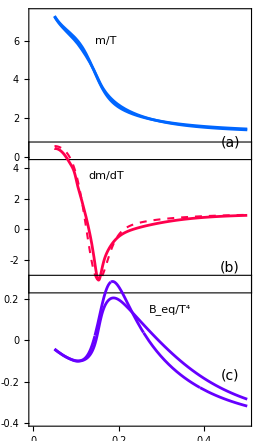
-Graphics-T (GeV)

```mathematica
legendz=Panel[Style["m/T",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendBeq=Panel[Style["B_eq/T^4",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legenddmdT=Panel[Style["dm/dT",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];

zstyle={Directive[RGBColor[0,0.4,1],AbsoluteThickness[2]]};
dmdTstyle={Directive[RGBColor[1,0,0.3],AbsoluteThickness[2]],Directive[RGBColor[1,0,0.3],AbsoluteThickness[1.5],AbsoluteDashing[Small]]};
Bstyle={Directive[RGBColor[0.4,0,1],AbsoluteThickness[2]]};

a = 25;
b= 30;

min = {0.0085,0};
maj={0.0145,0};

noTticks = {

{0.02,"",min},{0.04,"",min},{0.06,"",maj},{0.08,"",min},{0.1,"",maj},
{0.12,"",min},{0.14,"",min},{0.16,"",maj},{0.18,"",min},{0.2,"",maj},
{0.22,"",min},{0.24,"",min},{0.26,"",maj},{0.28,"",min},{0.3,"",maj},
{0.32,"",min},{0.34,"",min},{0.36,"",maj},{0.38,"",min},{0.4,"",maj},
{0.42,"",min},{0.44,"",min},{0.46,"",maj},{0.48,"",min},{0.5,"",maj}};

zplot=Plot[{zQuasifunc[T*5.067731],zold[T*5.06731]},{T,0.05,0.5},PlotRange->{{0,0.5},{0,7.5}},PlotStyle->zstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendz,{0.17,6}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{0.46,0.75}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dmdTplot=Plot[{mQuasifunc'[T*5.067731],mold'[T*5.067731]},{T,0.05,0.5},PlotRange->{{0,0.5},{-3.95,5.5}},PlotStyle->dmdTstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,noTticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legenddmdT,{0.17,3.5}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.46,-2.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot=Plot[{B0Quasifunc2[T*5.067731]/(T*5.067731)^4,Beqold[T*5.067731]/(T*5.067731)^4},{T,0.05,0.5},PlotRange->{{0,0.5},{-0.4,0.3}},PlotStyle->Bstyle,ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,All},{All,noTticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendBeq,{0.32,0.15}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{0.46,-0.17}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

quasi=Panel[GraphicsGrid[{{zplot},{dmdTplot},{Bplot}},Spacings->{0,-44.2}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{280,456}]

Export["quasi.pdf",quasi];
```

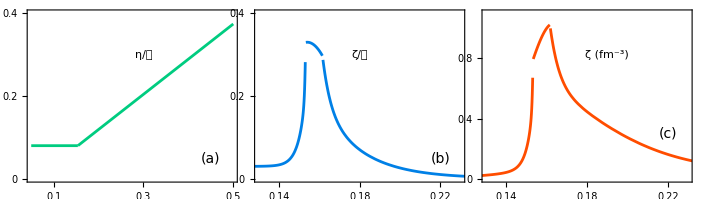
-Graphics-T (GeV)

```mathematica
legendηs=Panel[Style["η/𝒮",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendζs=Panel[Style["ζ/𝒮",FontSize->16,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendζ=Panel[Style["ζ (fm^-3)",FontSize->18,FontFamily->"Calibri"],Background->White,FrameMargins->0];

Tc = 0.154;
ηsmin = 0.08;
ηsslope =0.85;

ζsnorm = 1.25;
a0=-13.45;
a1=27.55;
a2=-13.77;
lambda1=0.9;
lambda2=0.25;
lambda3=0.9;
lambda4=0.22;
sigma1=0.025;
sigma2=0.13;
sigma3=0.0025;
sigma4=0.022;


ηsfunc[T_]=Piecewise[{

{ηsmin,T<Tc},
{ηsmin+ηsslope*(T-Tc),T≥Tc}
}];

ζsfunc[x_]=Piecewise[{
(* x = T/Tc*)
{lambda3*Exp[(x-1.0)/sigma3]+lambda4*Exp[(x-1.0)/sigma4]+0.03,x<0.995},
{(a0+a1*x+a2*x*x),0.995<x<1.05},
{lambda1*Exp[-(x-1.0)/sigma1]+lambda2*Exp[-(x-1.0)/sigma2]+0.001,x>1.05}
}];



etas =Plot[ηsfunc[T],{T,0.05,0.5},PlotRange->{{0.05,0.5},{0,0.4}},PlotStyle->Directive[RGBColor[0.0,0.8,0.5],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendηs,{0.3,0.3}],Inset[Style["(a)",FontSize->14,FontFamily->"Calibri"],{0.45,0.05}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

zetas =Plot[ζsfunc[T/Tc],{T,0.05,0.5},PlotRange->{{0.13,0.23},{0,0.4}},PlotStyle->Directive[RGBColor[0.0,0.5,0.9],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendζs,{0.18,0.3}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.22,0.05}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

zeta =Plot[ζsfunc[T/Tc]*Sfit[T*5.067731],{T,0.05,0.5},PlotRange->{{0.13,0.23},{0,1.1}},PlotStyle->Directive[RGBColor[1.0,0.3,0],AbsoluteThickness[2]],ImageSize->250,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendζ,{0.19,0.82}],Inset[Style["(c)",FontSize->14,FontFamily->"Calibri"],{0.22,0.3}]},ImagePadding->{{a,b},{Automatic,Automatic}}];


viscosity=Panel[GraphicsGrid[{{etas,zetas,zeta}},Spacings->{-20,0}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{700,210}]

Export["viscosity.pdf",viscosity];
```

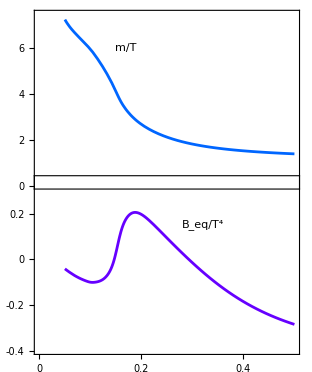
-Graphics-T (GeV)

```mathematica
zplot=Plot[{zQuasifunc[T*5.067731]},{T,0.05,0.5},PlotRange->{{0,0.5},{0,7.5}},PlotStyle->zstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,All}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendz,{0.17,6}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

dmdTplot=Plot[{mQuasifunc'[T*5.067731],mold'[T*5.067731]},{T,0.05,0.5},PlotRange->{{0,0.5},{-3.95,5.5}},PlotStyle->dmdTstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{noTticks,noTticks}},BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legenddmdT,{0.17,3.5}],Inset[Style["(b)",FontSize->14,FontFamily->"Calibri"],{0.46,-2.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

Bplot=Plot[{B0Quasifunc2[T*5.067731]/(T*5.067731)^4},{T,0.05,0.5},PlotRange->{{0,0.5},{-0.4,0.35}},PlotStyle->Bstyle,ImageSize->300,Frame->True,Axes->False,FrameTicks->{{All,All},{All,noTticks}},RotateLabel->False,BaseStyle->{FontSize->12},AspectRatio->0.75,Epilog->{Inset[legendBeq,{0.32,0.15}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

quasi=Panel[GraphicsGrid[{{zplot},{Bplot}},Spacings->{0,-44.9}],Style["T (GeV)",FontFamily->"Calibri",FontSize->14],{{Bottom,Center}},Background->White,ImageSize->{320,390}]

Export["quasi_big.pdf",quasi];
```

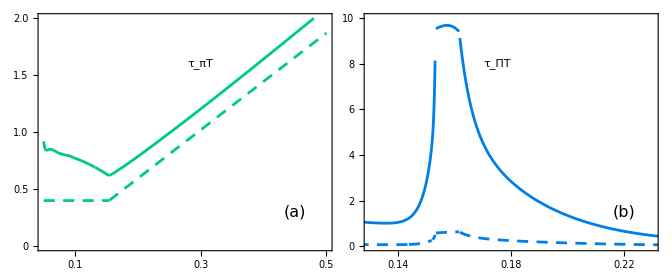
-Graphics-T (GeV)

```mathematica
legendtaupiT=Panel[Style["τ_πT",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];
legendtaubulkT=Panel[Style["τ_ΠT",FontSize->20,FontFamily->"Calibri"],Background->White,FrameMargins->0];

taupiT =Plot[{(ηsfunc[T]*(Equasi[T*5.067731]+Pquasi[T*5.067731]))/betapifit[T*5.067731],5.0*ηsfunc[T]},{T,0.05,0.5},PlotRange->{{0.05,0.5},{0,2}},PlotStyle->{Directive[RGBColor[0.0,0.8,0.5],AbsoluteThickness[2]],Directive[RGBColor[0.0,0.8,0.5],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]},ImageSize->350,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->13},AspectRatio->0.75,Epilog->{Inset[legendtaupiT,{0.3,1.6}],Inset[Style["(a)",FontSize->16,FontFamily->"Calibri"],{0.45,0.3}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

taubulkT=Plot[{(ζsfunc[T/Tc]*(Equasi[T*5.067731]+Pquasi[T*5.067731]))/betabulkfit[T*5.067731],ζsfunc[T/Tc]/(15.0*(1./3.-cs2fit[Equasi[T*5.067731]])^2)},{T,0.05,0.5},PlotRange->{{0.13,0.23},{0,10}},PlotStyle->{Directive[RGBColor[0.0,0.5,0.9],AbsoluteThickness[2]],Directive[RGBColor[0.0,0.5,0.9],AbsoluteThickness[2],AbsoluteDashing[{8,6}]]},ImageSize->350,Frame->True,Axes->False,FrameTicks->{{All,True},{All,All}},BaseStyle->{FontSize->13},AspectRatio->0.75,Epilog->{Inset[legendtaubulkT,{0.175,8}],Inset[Style["(b)",FontSize->16,FontFamily->"Calibri"],{0.22,1.5}]},ImagePadding->{{a,b},{Automatic,Automatic}}];

relaxation=Panel[GraphicsGrid[{{taupiT,taubulkT}},Spacings->{-20,0}],Style["T (GeV)",FontFamily->"Calibri",FontSize->16],{{Bottom,Center}},Background->White,ImageSize->{700,290}]

Export["relaxation.pdf",relaxation];
```